# Stochastic processes

We examine a few stochastic processes, and practice with random variables.

```mathematica
ClearAll["Global`*"]
```

Generate a pseudorandom real number between 0 and 2π.

```mathematica
RandomReal[{0,2Pi}]
```

#### Appropriate square function

We want to plot our solution in a square grid.

```mathematica
IdealSquare[xMin_,xMax_,yMin_,yMax_]:=Module[{},
dx=(xMax-xMin)/2;
cx=Mean[{xMin,xMax}];
dy=(yMax-yMin)/2;
cy=Mean[{yMin,yMax}];

Which[
dx≥dy,
yNewMin=cy-dx;yNewMax=cy+dx;{xMin,xMax,yNewMin,yNewMax},
dy>dx,
xNewMin=cx-dy;xNewMax=cx+dy;{xNewMin,xNewMax,yMin,yMax}
]
]
```

#### Walk functions

Here are a few ways a random walk could be generated.

```mathematica
randomGrid[]:=RandomChoice[{{{1},{0}},{{-1},{0}},{{0},{1}},{{0},{-1}}}];
randomPolar[]:=Module[{},t=RandomReal[{0,2Pi}];{{Cos[t]},{Sin[t]}}];
randomGridGeneral[n_]:=N[RandomChoice[{{Cos[(2Pi#)/n]},{Sin[(2Pi#)/n]}}&/@Range[n]]];
```

#### Random walk

We create a random walk function which takes in initial conditions, number of time-steps, and a fixed distance traveled per time-step governed by the walk functions before.

```mathematica
RandomWalk[init_,steps_,distance_,OptionsPattern[{plot->True,degrees->{1,-1},WalkSpace->randomPolar}]]:=Module[{},
solutions={init};
(* The purpose of degrees is to select a range of points with respect to degree away from the first. *)

{start,end}=OptionValue[degrees];

curStep=2;

(* To ensure that our final plot has a 1:1 coordinate ratio, we find the smallest and largest x and y values, respectively. *)
xMin=init[[1]];
xMax=init[[1]];
yMin=init[[2]];
yMax=init[[2]];

direction=OptionValue[WalkSpace];

While[curStep≤steps,
curSol=solutions[[curStep-1]];
dir=direction[];
newSol=curSol+distance direction[];

(* xMin, xMax, yMin, yMax are re-evaluated at every iteration. *)
xMin=Min[xMin,newSol[[1]]];
xMax=Max[xMax,newSol[[1]]];
yMin=Min[yMin,newSol[[2]]];
yMax=Max[yMax,newSol[[2]]];
AppendTo[solutions,newSol];
curStep+=1];

(* Calculate ideal square. *)
{xMin,xMax,yMin,yMax}=IdealSquare[xMin,xMax,yMin,yMax];

solutions=Level[solutions[[#]],{-1}]&/@Range[steps];
If[OptionValue[plot],
ListPlot[
solutions[[start;;end]],
AspectRatio->1,
(*Axes->False,*)
ImageSize->1024,
Joined->True,
PlotRange->{{xMin,xMax},{yMin,yMax}},
PlotStyle->Gray
],
{solutions[[start;;end]],xMin,xMax,yMin,yMax}]
]
```

#### Experiments with RandomWalk

A random walk of 10,000 steps, using randomPolar.

```mathematica
RandomWalk[{{0},{0}},10000,1]
```

A random walk of 10,000 steps, using randomGrid orientations.

```mathematica
RandomWalk[{{0},{0}},10000,1,WalkSpace->randomGrid]
```

A random walk of 10,000 steps, in which the possible walk orientations are {0,(2π)/3,(4π)/3}.

```mathematica
RandomWalk[{{0},{0}},10000,1,WalkSpace->(randomGridGeneral[3]&)]
```

#### Density of a random walk

Perhaps we are less concerned about the path, and more about the points traversed by many walks. What does the point distribution look like for 10,000 walks?

```mathematica
With[{packages=RandomWalk[{{0},{0}},10,1,plot->False]&/@Range[10000]},
{solutions,xMins,xMaxs,yMins,yMaxs}=Transpose[packages];
solutions=Flatten[solutions,1];
xMin=Min[xMins];
xMax=Max[xMaxs];
yMin=Min[yMins];
yMax=Max[yMaxs];
{xMin,xMax,yMin,yMax}=IdealSquare[xMin,xMax,yMin,yMax];

Show[
ListPlot[
solutions,
AspectRatio->1,
ImageSize->1024,
PlotRange->{{xMin,xMax},{yMin,yMax}},
PlotStyle->{Opacity[.5],Gray}
]]]
```

## Stochastic differential equations

We compute some solutions to the SDE ⅆx=sin xⅆt+sin tⅆW, where W(t) is a standard 
Wiener process.

```mathematica
ClearAll["Global`*"]
```

```mathematica
proc=ItoProcess[ⅆx[t]==Sin[x[t]]ⅆt+Sin[t]ⅆw[t],x[t],{x,0},t,w\[Distributed]WienerProcess[]]
```

ItoProcess[{{Sin[x[t]]},{{Sin[t]}},x[t]},{{x},{0}},{t,0}]

TemporalData[…]

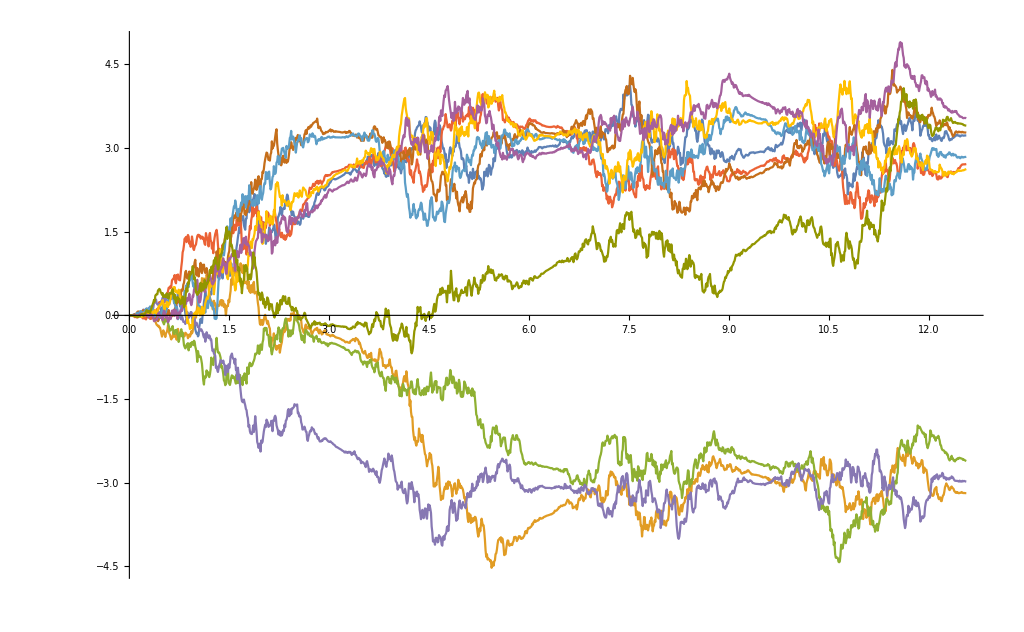

```mathematica
RandomFunction[proc,{0,4Pi,.01},10]
ListLinePlot[%,GridLines->{(Pi#)&/@Range[3],{-Pi,Pi}},ImageSize->1024]
```